## Fig. S1D and S1E

Set L=20  to generate plots for S1D, and  L=30 to generate S1E.

```mathematica
Clear["Global`*"];
```

```mathematica
l=20;
figName=If[l==20,"D","E"];
```

```mathematica
precision=30;
$MinPrecision=precision;
SetDirectory[NotebookDirectory[]];
```

### Statics

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]  
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)

fullConcentration[n_,nutrient_]:=
Block[{a,b,c,coeff,positions,pieces,conditions,fullC},
coeff=getConcentration[n,nutrient];
positions=getPositions[n];
a=Table[coeff[[2*i-1]],{i,m}];
b=Table[coeff[[2*i]],{i,m}];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
pieces=Table[c[a[[j]],b[[j]],α[[j,nutrient]],theta-positions[[j,1]]],{j,m}];
conditions=Table[positions[[i,1]]<theta<=positions[[i,2]],{i,m}];
fullC=Piecewise[Transpose[{pieces,conditions}]]
];
```

### Define some constants

```mathematica
supply=1;  (*total nutrient supply*)
δ=supply;
e=1;             (* total enzyme budget*)
steps=(10^6);
```

### Numeric parameters

```mathematica
d=1; //N(*diffusion coefficient*)
s1=0.5;
s2=1-s1;
s={s1,s2}*supply;
```

```mathematica
SeedRandom[100];
alphas=RandomReal[e,10];
α=Table[{alphas[[i]],e-alphas[[i]]},{i,Length[alphas]}];
```

```mathematica
m=Length[α];
strat=Table[α[[i,1]],{i,m}];   (*maps strategies to continuum of nutrient 1, nutrient 2*)
sScaled=(e/Total[s])*s[[1]];
```

### Dynamics

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,2}]//Total
];
```

```mathematica
ndot[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
n0=n0/.{x_/;x<10^-8->0};
cCoeff=Transpose[{getConcentration[n0,1],getConcentration[n0,2]}];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];
```

### Calculate n_σ(t) and plot

```mathematica
nInit=l*ConstantArray[1/m,m]//N;
```

```mathematica
AbsoluteTiming[sol=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit},n,{t,0,steps}]];
```

```mathematica
colors=Table[ColorData[97,i],{i,m}];
p=Table[{Graphics[{EdgeForm[{Black}],FaceForm[colors[[i]]],Disk[]}],.05},{i,m}];
```

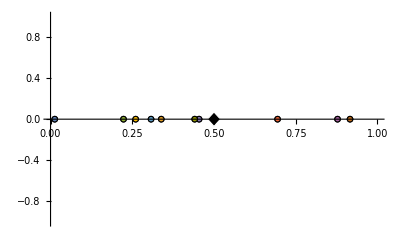

```mathematica
Show[ListPlot[Table[{{strat[[i]],0}},{i,m}],Axes->{True,False},AxesStyle->Thick,Ticks->{0,.2,.4,.6,.8,1},PlotMarkers->p,TicksStyle->Directive[Black,12],PlotRange->{{0,1},Automatic}],Graphics[{EdgeForm[{White}],Polygon[{{.5-.02,0},{.5,.07},{.5+.02,0},{.5,-.07}}]}],Method->{"AxesInFront"->False}]
```

```mathematica
Export["figS1E_strategies.svg",%];
```

```mathematica
c1Final=fullConcentration[sol[sol["Domain"][[1,2]]],1];
c2Final=fullConcentration[sol[sol["Domain"][[1,2]]],2];
finalPositions=getPositions[sol[sol["Domain"][[1,2]]]];
```

### Final Concentration

```mathematica
rT[theta_]:=
Block[{conditions,pieces},
pieces=Table[Total[Table[s[[i]]/α[[j,i]],{i,Length[s]}]],{j,m}];
conditions=Table[finalPositions[[i,1]]<theta≤finalPositions[[i,2]],{i,m}];
Piecewise[Transpose[{pieces,conditions}]]
]
```

```mathematica
ri[x_,nutrient_]:=Block[{conditions,pieces},
pieces=Table[s[[nutrient]]/α[[j,nutrient]],{j,m}];
conditions=Table[finalPositions[[i,1]]<theta≤finalPositions[[i,2]],{i,m}];
Piecewise[Transpose[{pieces,conditions}]]
]
```

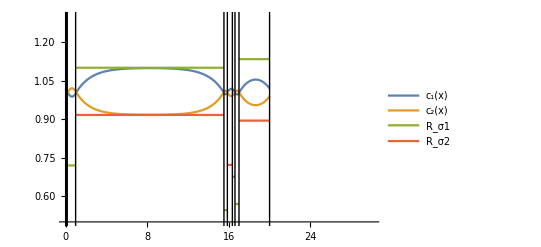

```mathematica
dividers2=Table[Line[{{finalPositions[[i,2]],-1},{finalPositions[[i,2]],5}}],{i,m}];
Plot[{c1Final,c2Final,ri[theta,1],ri[theta,2]},{theta,0,l},PlotRange->{{0,30+.1},{.5,1.3}},
Epilog->{dividers2},TicksStyle->Directive[Black, 12],PlotLegends->{"c_1(x)","c_2(x)","R_σ1","R_σ2"},LabelStyle->Directive[Black,12]]
```

```mathematica
Export["figS1"<>figName<>"_L"<>ToString[l]<>"_concentration.svg",%];
```